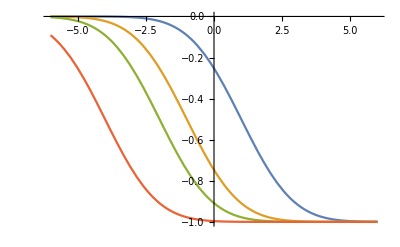

```mathematica
Plot[Table[-CDF[NormalDistribution[-μ,1.5],x],{μ,{-1,1,2,4}}]//Evaluate,{x,-6,6}]
```

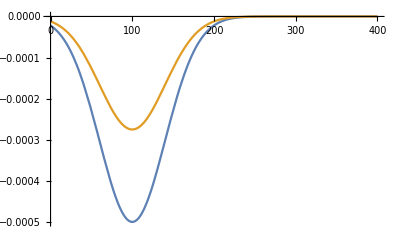

```mathematica
With[{σ=40, μ=100},Plot[{-(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)(0.05) ,-(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)(0.55)(0.05)}, {x,0,400}]]
```

```mathematica
f[x_]:= If[x<118, -0.0017,-ArcCot[x]/5]
```

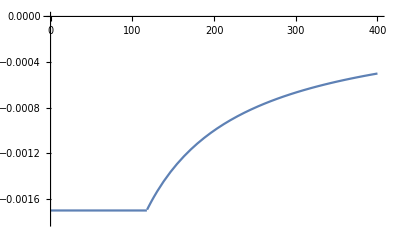

```mathematica
Plot[f[x],{x,00,400}, PlotRange->{-0.0018,0}]
```

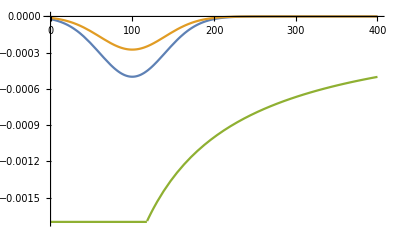

```mathematica
With[{σ=40, μ=100},Plot[{-(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)(0.05) ,-(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)(0.55)(0.05), f[x]}, {x,0,400}]]
```

```mathematica
With[{σ=40, μ=100},Plot3D[f[x]+ -(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)(0.05) LegendreP[2, Cos[θ]] + -(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)(0.55)(0.05) LegendreP[4, Cos[θ]],{x,0,400},{θ,0,π}]]
```

-Graphics3D-

```mathematica
g=Interpolation[{{0, -0.0018},{25, -0.0018},{50, -0.0018},{100,-0.00175},{200,-.0014},{300,-.0007},{400,-0.0005},{500,-0.00049}}, InterpolationOrder->3]
```

InterpolatingFunction[…]

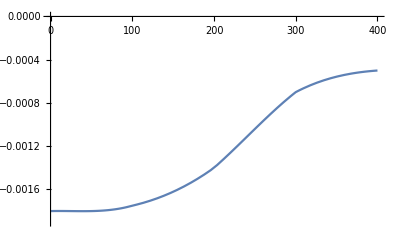

```mathematica
Plot[g[x],{x,0.,400.}, PlotRange->{-0.0019,0}]
```

```mathematica
With[{σ=40, μ=100},Plot3D[g[x]+ -(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)(0.05) LegendreP[2, Cos[θ]] + -(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)(0.55)(0.05) LegendreP[4, Cos[θ]],{x,0,400},{θ,0,π}]]
```

-Graphics3D-

```mathematica
g[x]
```

InterpolatingFunction[…][x]

```mathematica
∂_x %119
```

InterpolatingFunction[…][x]

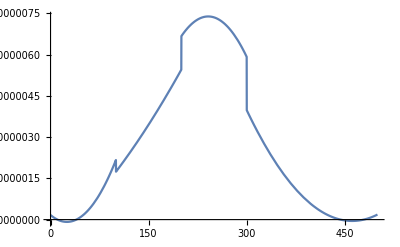

```mathematica
Plot[%120,{x,0.,500.}]
```